## 1. Select a metal and find its dielectric properties in the literature at several wavelengths. Choose a prism material and find its refractive index in the literature at the same wavelengths.

```mathematica
nkLithium=Import["C:\\Users\\User\\iCloudDrive\\Documents\\Univer\\11th_semester_nanoplasmonics\\Rasigni.csv","CSV"];

ReϵLithium=Table[{1000*nkLithium[[i]][[1]],
(nkLithium[[i]][[2]])^2-(nkLithium[[38+i]][[2]])^2},{i,2,36}];
ImϵLithium=Table[{10^-6*nkLithium[[i]][[1]],
2*(nkLithium[[i]][[2]])*(nkLithium[[38+i]][[2]])},{i,2,36}];

nSilica=Import["C:\\Users\\User\\iCloudDrive\\Documents\\Univer\\11th_semester_nanoplasmonics\\Arosa.csv","CSV"];
```

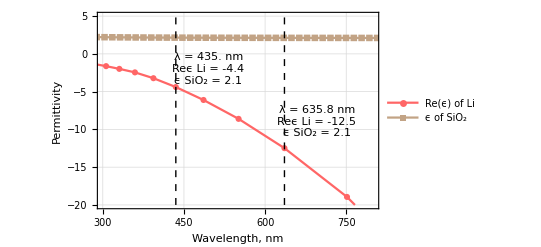

```mathematica
nLithium=Table[{1000*nkLithium[[i]][[1]],nkLithium[[i]][[2]]},{i,2,36}];
ϵSilica=Table[{1000*nSilica[[i]][[1]],(nSilica[[i]][[2]])^2},{i,2,50}];

ListPlot[{ReϵLithium,ϵSilica},PlotRange->{{300,800},{-20,5}},GridLinesStyle->Directive[Dashed, Gray],GridLines->Automatic,
Joined->True,
PlotMarkers->Automatic,
Epilog->{
{
Dashed,
Line[
{{ReϵLithium[[30]][[1]],-20},
{ReϵLithium[[30]][[1]],5}}
]
},
Text[
Column[
{
Style["λ = " <> ToString[ReϵLithium[[30]][[1]]"nm"],Small, Black, FontFamily->"Times New Roman"],
Style["Reϵ Li = " <> ToString[Round[ReϵLithium[[30]][[2]],.1]],Small, Lighter[Red,0.4], FontFamily->"Times New Roman"],
Style["ϵ SiO_2 = " <> ToString[Round[ϵSilica[[30]][[2]],.1]],Small, Lighter[Brown,0.4], FontFamily->"Times New Roman"]
}
],
{ReϵLithium[[30]][[1]]+60,-9}
],
{
Dashed,
Line[
{{ReϵLithium[[27]][[1]],-20},
{ReϵLithium[[27]][[1]],5}}
]
},
Text[
Column[
{
Style["λ = " <> ToString[ReϵLithium[[27]][[1]]"nm"],Small, Black, FontFamily->"Times New Roman"],
Style["Reϵ Li = " <> ToString[Round[ReϵLithium[[27]][[2]],.1]],Small, Lighter[Red,0.4], FontFamily->"Times New Roman"],
Style["ϵ SiO_2 = " <> ToString[Round[ϵSilica[[27]][[2]],.1]],Small, Lighter[Brown,0.4], FontFamily->"Times New Roman"]
}
],
{ReϵLithium[[27]][[1]]+60,-2}
]
},
PlotTheme->"Scientific",
Frame->True,
FrameLabel->{
"Wavelength, nm" ,
"Permittivity"
},
FrameStyle->Directive[Black,Medium],
PlotLegends->Placed[
{"Re(ϵ) of Li","ϵ of SiO_2"}, 
{0.45,0.2}
],
PlotStyle->{Lighter[Red,0.4],Lighter[Brown,0.4]}
]
```

## 2. Calculate the angular dependence of the reflection coefficient in the Kretschmann configuration for the selected metal and prism at the chosen wavelengths. Assume that air is present at the outer boundary of the film.

```mathematica
λ1=ReϵLithium[[27]][[1]]*10^-9;
λ2=ReϵLithium[[5]][[1]]*10^-9;

ReϵLi1=ReϵLithium[[27]][[2]];
ImϵLi1=ImϵLithium[[27]][[2]];
ϵLi1=ReϵLi1+ⅈ*ImϵLi1;

ReϵLi2=ReϵLithium[[30]][[2]];
ImϵLi2=ImϵLithium[[30]][[2]];
ϵLi2=ReϵLi2+ⅈ*ImϵLi2;

d=50*10^-9;
ϵSiO=2.1;
ϵAir=1^2;

k1[θ_]:=2 π/λ1 Sqrt[ϵSiO]Cos[θ];
k2[θ_]:=2 π/λ1 Sqrt[ϵLi1-ϵSiO*(Sin[θ])^2];
k3[θ_]:=2 π/λ1 Sqrt[ϵAir-ϵSiO*(Sin[θ])^2];
rp12[θ_]:=(ϵLi1*k1[θ]-ϵSiO*k2[θ])/(ϵLi1*k1[θ]+ϵSiO*k2[θ]);
rp23[θ_]:=(ϵAir*k2[θ]-ϵLi1*k3[θ])/(ϵAir*k2[θ]+ϵLi1*k3[θ]);
rs12[θ_]:=(k1[θ]-k2[θ])/(k1[θ]+k2[θ]);
rs23[θ_]:=(k2[θ]-k3[θ])/(k2[θ]+k3[θ]);

exponent[θ_]:=ⅇ^(2*ⅈ*k2[θ]*d);

Rp[θ_]:=(Abs[(rp12[θ]+rp23[θ]*exponent[θ])/(1+rp12[θ]*rp23[θ]*exponent[θ])])^2;
Rs[θ_]:=(Abs[(rs12[θ]+rs23[θ]*exponent[θ])/(1+rs12[θ]*rs23[θ]*exponent[θ])])^2;
```

```mathematica
Manipulate[Module[{Rp,Rs,ϵLi1,ReϵLi1,ImϵLi1},
ReϵLi1=ReϵLithium[[i]][[2]];
ImϵLi1=ImϵLithium[[i]][[2]];
ϵLi1=ReϵLi1+ⅈ*ImϵLi1;Rp[θ_]:=(Abs[((ϵLi1*2 π/(ReϵLithium[[i]][[1]]*10^-9)Sqrt[ϵSiO]Cos[θ]-ϵSiO*2 π/(ReϵLithium[[i]][[1]]*10^-9)Sqrt[ϵLi1-ϵSiO*(Sin[θ])^2])/(ϵLi1*2 π/(ReϵLithium[[i]][[1]]*10^-9)Sqrt[ϵSiO]Cos[θ]+ϵSiO*2 π/(ReϵLithium[[i]][[1]]*10^-9)Sqrt[ϵLi1-ϵSiO*(Sin[θ])^2])+((ϵAir*2 π/(ReϵLithium[[i]][[1]]*10^-9)Sqrt[ϵLi1-ϵSiO*(Sin[θ])^2]-ϵLi1*2 π/(ReϵLithium[[i]][[1]]*10^-9)Sqrt[ϵAir-ϵSiO*(Sin[θ])^2])/(ϵAir*2 π/(ReϵLithium[[i]][[1]]*10^-9)Sqrt[ϵLi1-ϵSiO*(Sin[θ])^2]+ϵLi1*2 π/(ReϵLithium[[i]][[1]]*10^-9)Sqrt[ϵAir-ϵSiO*(Sin[θ])^2]))*ⅇ^(2*ⅈ*2 π/(ReϵLithium[[i]][[1]]*10^-9)Sqrt[ϵLi1-ϵSiO*(Sin[θ])^2]*d))/(1+((ϵLi1*2 π/(ReϵLithium[[i]][[1]]*10^-9)Sqrt[ϵSiO]Cos[θ]-ϵSiO*2 π/(ReϵLithium[[i]][[1]]*10^-9)Sqrt[ϵLi1-ϵSiO*(Sin[θ])^2])/(ϵLi1*2 π/(ReϵLithium[[i]][[1]]*10^-9)Sqrt[ϵSiO]Cos[θ]+ϵSiO*2 π/(ReϵLithium[[i]][[1]]*10^-9)Sqrt[ϵLi1-ϵSiO*(Sin[θ])^2]))*((ϵAir*2 π/(ReϵLithium[[i]][[1]]*10^-9)Sqrt[ϵLi1-ϵSiO*(Sin[θ])^2]-ϵLi1*2 π/(ReϵLithium[[i]][[1]]*10^-9)Sqrt[ϵAir-ϵSiO*(Sin[θ])^2])/(ϵAir*2 π/(ReϵLithium[[i]][[1]]*10^-9)Sqrt[ϵLi1-ϵSiO*(Sin[θ])^2]+ϵLi1*2 π/(ReϵLithium[[i]][[1]]*10^-9)Sqrt[ϵAir-ϵSiO*(Sin[θ])^2]))*ⅇ^(2*ⅈ*2 π/(ReϵLithium[[i]][[1]]*10^-9)Sqrt[ϵLi1-ϵSiO*(Sin[θ])^2]*d))])^2;
k1[θ_]:=2 π/λ1 Sqrt[ϵSiO]Cos[θ];
k2[θ_]:=2 π/λ1 Sqrt[ϵLi1-ϵSiO*(Sin[θ])^2];
k3[θ_]:=2 π/λ1 Sqrt[ϵAir-ϵSiO*(Sin[θ])^2];
exponent[θ_]:=ⅇ^(2*ⅈ*k2[θ]*d);
rs12[θ_]:=(k1[θ]-k2[θ])/(k1[θ]+k2[θ]);
rs23[θ_]:=(k2[θ]-k3[θ])/(k2[θ]+k3[θ]);
Rs[θ_]:=(Abs[(rs12[θ]+rs23[θ]*exponent[θ])/(1+rs12[θ]*rs23[θ]*exponent[θ])])^2;
Plot[{Rp[θ],Rs[θ]},{θ,0,π/2},
PlotRange->{{0,π/2},{0,1.1}},
PlotStyle->{Lighter[Brown,0.4],Lighter[Red,0.4]},
GridLinesStyle->Directive[Dashed, Gray],
GridLines->Automatic,
Frame->True,
FrameLabel->{
"Incidence angle, deg" ,
"Reflection coefficient"
},
FrameStyle->Directive[Black,Medium],
FrameTicks->{{Automatic,None},{Table[{n π/8,Row[{N[n 180/8],"°"}]},{n,0,4}],None}},
PlotTheme->"Scientific",
PlotLegends->Placed[
{"p-polarized","s-polarized"}, 
{0.81,0.18}
],
Epilog->{Text[Column[{
Style["λ = " <> ToString[Round[ReϵLithium[[i]][[1]],1]] "nm",Medium,Black, FontFamily->"Times New Roman"],
Style["d = " <> ToString[d *10^9] "nm",Medium,Black, FontFamily->"Times New Roman"]
}],{0.2,0.9}]}(*,
PlotLabel->"Reflection coefficient vs. Angle of incidence (Kretschmann configuration)"*)
]],
{{i,27, "Wavelength, nm"},2,Length[ReϵLithium],1},
Dynamic[Text[ToString[Round[ReϵLithium[[i]][[1]],1]]]],
{{d,50*10^-9,"Film width, nm"},10^-8,10^-7,10^-9},
Dynamic[Text[ToString[Round[d*10^9,1]]]]
]
```

## 3. Develop a sensor based on surface plasmon excitation in thin-film structures using the Kretschmann configuration.

```mathematica
(*Define parameters*)λ=700*10^-9;(*Wavelength in meters (e.g.,red laser)*)nPrism=1.515;(*Refractive index of BK7 glass prism*)nAir=1.0;(*Refractive index of air*)dMetal=50*10^-9;(*Metal film thickness in meters*)(*Define Drude model for noble metal (e.g.,gold)*)DrudeModel[ωp_,γ_,ω_]:=1-(ωp^2/(ω^2+I γ ω));

(*Plasma frequency (rad/s) and damping for Au*)
ωpAu=1.37*10^16;
γAu=4.05*10^13;
Manipulate[
(*Define dielectric function for pure gold and doped gold*)
εAu[ω_]:=DrudeModel[ωpAu,γAu,ω];
εDopedAu[ω_]:=DrudeModel[ωpAu*(1-dope),γAu*(1+dope),ω];(*Simulating dopant effect*)(*Convert wavelength to frequency*)ω0=2 π c/λ/. {c->3*10^8};

(*Calculate dielectric constants at λ*)
εMetalPure=εAu[ω0];
εMetalDoped=εDopedAu[ω0];

(*Reflection coefficient function (Fresnel equations for p-polarized light)*)
ReflectionCoefficient[n1_,n2_,θ_,εMetal_]:=Module[{k0,kx,kz1,kz2,r},k0=2 π/λ;
kx=k0*n1*Sin[θ];
kz1=Sqrt[(k0*n1)^2-kx^2];
kz2=Sqrt[(k0^2*εMetal)-kx^2];
r=(εMetal*kz1-n1^2*kz2)/(εMetal*kz1+n1^2*kz2);
Abs[r]^2];

(*Compute reflectivity for a range of angles*)
angles=Range[0,90,0.1];(*Incident angles in degrees*)reflectivityPure=Table[{θ,ReflectionCoefficient[nPrism,nAir,θ Degree,εMetalPure]},{θ,angles}];

reflectivityDoped=Table[{θ,ReflectionCoefficient[nPrism,nAir,θ Degree,εMetalDoped]},{θ,angles}];

(*Plot reflection spectra to observe SPR shift*)
ListLinePlot[{reflectivityPure,reflectivityDoped},
PlotStyle->{Lighter[Brown,0.4],Lighter[Red,0.4]},
PlotLegends->Placed[{"Pure Au","Doped Au"},{0.2,0.15}],
AxesLabel->{"Angle (°)","Reflectivity"},
GridLines->Automatic,
Frame->True,
FrameLabel->{"Incident Angle (°)","Reflectivity"},
(*PlotLabel->"SPR Shift Due to Doping in Gold",*)
Epilog->{Text[Column[{
Style["λ = " <> ToString[λ*10^9] "nm",Medium,Black],
Style["d = " <> ToString[dMetal *10^9] "nm",Medium,Black],
Style["dope = " <> ToString[Round[dope *100,1]] <>"%",Medium,Black]
}],{15,0.997}]}],
{{dope,0.1,"Dope fraction"},0.01,0.5,Appearance->"Labeled"}
]
```